CHAPTER ChapterLabel

Financial Engineering

I’ve got the brains, you’ve got the looks
Let’s make lots of money
You’ve got the brawn, I’ve got the brains
Let’s make lots of money

Pet Shop Boys, “Opportunities (Let’s Make
Lots of Money)”

ChapterLabel.Heading1  Introduction

Financial engineering (also known as computational finance) is the use of computers to create mathematical models and simulations that attempt to price financial instruments, model their sensitivity to changes in the market, hedge against these changes, and measure and manage risk. This is a high-stakes game, where there can be great reward for getting things right but even greater loss if you get things wrong. This became acutely evident during the financial crisis that started around July 2007. It might be tempting to conclude that attempts to bring mathematical rigor to the chaos of the market is foolhardy, but this would be like concluding that traditional engineering is foolhardy because a plane crashed or a bridge fell. Such failings are human failings, not mathematical ones. They only point to the need to use computational tools more diligently and more responsibly.

One goal for this chapter was to create a variety of recipes with a range of difficulties. This means that there are some recipes that may seem trivial and others that a novice might find difficult. Almost every recipe tries to demonstrate techniques that are unique to Mathematica; I hope readers of every skill level will take away techniques that they can apply to financial problems that interest them.

Mathematica has unique characteristics lacking in many other tools commonly used in the financial industry. As of version 6, Mathematica has integrated financial data that is essential to testing your models. This is a big plus; having worked in the industry, I have seen how hard it can be for quants (quantitative analysts) to get data easily that is immediately usable. This may seem counterintuitive; it seems that investment banks and hedge funds would be swimming in data. They are, but you often must exert great effort to access it because of technical, logistical, and political barriers. Recipe 14.1 explains how to use FinancialData to get access to historical and delayed market data. Unfortunately, FinancialData is still incomplete. As of version 7, it concentrates mainly on equities, commodities, and currency data. There is nothing related to government, municipal, or corporate bonds; options; or interest rates. Luckily, Mathematica will import data from other sources; Recipe 14.2 shows an example of that.

Another important feature of Mathematica is its ability to find exact solutions using its unparalleled symbolic capabilities. Exact solutions, when you can get them, overcome the errors and inaccuracies introduced by numerical methods, especially around the boundaries of a solution. For example, when computing Greeks it is advantageous if you can compute a symbolic derivative (D) rather than a numerical one (ND). Recipe 14.6 shows how the symbolic capabilities of Mathematica can be used to compute and visualize the Greeks for European style options. See the introductory sidebar on page 551 if this is all Greek to you!

Performance is important in financial engineering, and getting Mathematica to perform well can be tricky for the novice. Recipes 14.8, 14.9, and 14.10 show how to use some of the optimized special functions that execute at machine speed and how to use Compile to eliminate the overhead of handwritten interpreted code. When writing numerically intense financial functions, you should try to compile as much as possible, but there are cases where functions cannot be compiled fully and where doing so may influence results.

Finally, Mathematica has some of the best visualization tools for checking your models and developing an intuition for their behaviors across different regions of the solution. Almost every recipe includes 2D or 3D plots, but Recipe 14.12 shows how you can use lower-level graphics primitives to create useful diagrams.

A Brief Introduction to Computational Finance for the Nonquant

It is impossible to do justice to this topic in a few paragraphs, but since this is a general purpose book and computational finance is littered with specific terminology, I attempt to define some basic ideas that are assumed in the recipes in the book. The references below can help you dig deeper.

Bonds are debt instruments that allow the lending of money under set terms. Typically, the issuer (borrower) of a bond is obligated to pay the holder (lender) interest in the form of fixed payments at specified dates (the coupon). A wide variety of terms are associated with various bonds that influence the computation of price, yield, risk characteristics, and so forth. Some bonds may be convertible to a different security (e.g., common stock) and some may be callable (the issuer can cancel their obligation by paying back the holder before the bonds expire). A fixed-rate bond is initially issued at a set price for a standardized amount (e.g., 1000 × $100.00) at a set interest rate (e.g., 6%). After the bond is issued, its price fluctuates (based on factors such as interest rates, credit ratings, and so forth). The change in price alters the bond’s yield or effective interest rate, since the interest remains fixed. So, for example, if the bond was issued at $100 but falls to $95, its yield would increase because a buyer would be getting the same interest payments for less up-front cost. Thus, price and yield have an inverse relation.

An option on a security is a contract that gives the holder the right (but not the obligation) to buy or sell that stock at a specific price (the strike price) on a specific date. The owner of a call has the right to buy; the owner of a put has the right to sell to the buyer. In contrast, the seller of a call is obligated to sell the security at the strike if it is exercised by the owner, and the seller of the put is obligated to buy. It would only make sense for an owner of an option to exercise it if it were in the money, if the option’s strike were favorable relative to the market price of the underlying security. For example, a call for IBM at strike $100 would be favorable to the call owner if IBM were trading at $120 when the call was exercised: there would be an immediate profit of $20 less transaction fees.

Options come in different flavors. European options can only be exercised at the expiration date. These are the simplest to model. American options can be exercised at any time up to expiration. If the underlying security pays dividends, it creates further complications that must be accounted for in the model. There are also more exotic flavors of options, such as Asian and Bermudian, that you can read about in the references.

The Greeks are important measures for an options trader. The Greeks are computed as derivatives of the option’s pricing function with respect to various parameters. For example, delta is the derivative with respect to the price of the underlying security. Thus, delta measures the sensitivity of the option’s price with respect to changes in the underlying. Gamma is a second derivative with respect to price and measures the sensitivity of delta. Other important Greeks are theta (time), rho (interest rates), and vega (volatility). These are discussed in Recipe 14.6.

See Also

The classic text in this area is Options, Futures, and Other Derivatives by John C. Hull (Prentice Hall).

The Wilmott Journal and magazine discuss modern ideas in quantitative finance:
http://bit.ly/rm9hO.

If you have more of a passing interest, Wikipedia has good definitions and basic
explanations of most of the ideas discussed here.

An excellent book that teaches Mathematica programming in parallel with financial engineering is Computational Financial Mathematics Using Mathematica by Srdjan Stojanovic^(.b4) (Springer).

ChapterLabel.Heading1  Leveraging Mathematica’s Bundled Financial Data

Problem

You need financial data to test your mathematical models.

Solution

Use Mathematica’s curated financial data, FinancialData. This is a data source that you can query to extract quite a variety of up-to-date data (15-minute delayed and historical) on a variety of security types, what Mathematica calls "Groups". To see the available groups, execute the following. If this is the first time you are doing this, you will see the status message "Initializing Financial Indices", and the groups will display.

```mathematica
FinancialData["Groups"]
```

{Currencies,Exchanges,ExchangeTradedFunds,Futures,Indices,MutualFunds,Sectors,Stocks}

The next thing you will want to find is the available properties of the data.

```mathematica
FinancialData["Properties"]
```

{Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,CUSIP,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EBITDA,Exchange,FloatShares,ForwardEarnings,ForwardPERatio,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,ISIN,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Name,Open,PEGRatio,PERatio,Price,PriceTarget,PriceToBookRatio,PriceToSalesRatio,QuarterForwardEarnings,Range,Range52Week,RawClose,RawHigh,RawLow,RawOpen,RawRange,Return,Sector,SEDOL,ShortRatio,SICCode,StandardName,Symbol,Volatility20Day,Volatility50Day,Volume,Website,YearEarningsEstimate,YearPERatioEstimate}

Now you can retrieve data for a specific symbol. By default, you will get the current price, but you can also ask for data from a specific date or within a date range.

```mathematica
FinancialData["IBM","Price"]
```

127.17

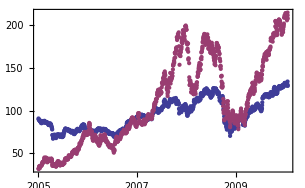

```mathematica
DateListPlot[{FinancialData["IBM","Price","Jan 1,2005"],FinancialData["AAPL","Price","Jan 1,2005"]}]
```

Discussion

FinancialData has a rich interface that allows you to perform many types of queries. First, let’s see how you can use the interface to find what is available. Suppose you are curious to see what coverage there is for a specific symbol.

```mathematica
FinancialData["IBM","Properties"]
```

{Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,CUSIP,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EBITDA,Exchange,FloatShares,ForwardEarnings,ForwardPERatio,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,ISIN,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Name,Open,PEGRatio,PERatio,Price,PriceTarget,PriceToBookRatio,PriceToSalesRatio,QuarterForwardEarnings,Range,Range52Week,RawClose,RawHigh,RawLow,RawOpen,RawRange,Return,Sector,SEDOL,ShortRatio,SICCode,StandardName,Symbol,Volatility20Day,Volatility50Day,Volume,Website,YearEarningsEstimate,YearPERatioEstimate}

One difficulty is that every security is not guaranteed to have every property populated. There seem to be two possibilities when a property is not present. You may get Missing["NotAvailable"] or you may get an unevaluated expression like FinancialData["IBM", "CumulativeFractionalChange"]. One way to see what properties are populated and also get a sample of the associated data is to execute the following (I elide the results with Short).

```mathematica
With[{sec="IBM"},
Select[
Table[{prop,FinancialData[sec,prop]},{prop,FinancialData[sec,"Properties"]}],FreeQ[#,{_,Missing["NotAvailable"]|HoldPattern[FinancialData[__]]}]&]]//Short
```

{{Average200Day,122.097},{Average50Day,129.82},«54»,{YearEarningsEstimate,11.08},{YearPERatioEstimate,11.64}}

Let’s look at other types of financial data and see some of the additional capabilities that are provided. Industry sectors are especially useful for studying and comparing different industries’ performance.

```mathematica
Length[FinancialData["Sectors"]]
```

169

There are 169 sectors. Here I use a pattern to find those with the string "Service" in the name.

```mathematica
Select[FinancialData["Sectors"],StringMatchQ[#,__~~"Service"~~__]&]
```

{CommunicationsServicesNotElsewhere,LegalServices,MiscellaneousBusinessServices,MiscellaneousHealthAndAlliedServicesNot,OilNaturalGasFieldServices,RefrigerationServiceMachinery,ResearchDevelopmentAndTestingServices,TruckingAndCourierServicesExceptAir}

Given a sector, you can ask for its members. You can also use "Members" with an
index, such as the S&P 500, or an exchange like the New York Stock Exchange (NYSE). Here I pick 10 OilNaturalGasFieldServices members at random.

```mathematica
RandomChoice[FinancialData["OilNaturalGasFieldServices","Members"],10]
```

{DE:HRL,PK:ONXC,PK:ASRPF,F:SJR,PK:VTHC,F:DG1,NYSE:WG,TO:POU,TO:POU,DE:DO1}

```mathematica
Mean[Select[Quiet[FinancialData[#,"Price"]& /@ FinancialData["OilNaturalGasFieldServices","Members"]],NumberQ]]
```

13.025

FinancialData provides information on 153 currencies. You can get the exchange rate by using a string or list notation.

```mathematica
Length[FinancialData["Currencies"]]
```

153

```mathematica
FinancialData["USD/EUR"]
```

0.7065

```mathematica
FinancialData[{"USD","EUR"}]
```

0.7065

FinancialData does not provide a notation to get more than a single property at a time, which is unfortunate. You can use Outer to get this behavior, but it seems it could be done more efficiently if this were native to FinancialData. First I extract U.S. oil and gas service companies using FinancialData’s ability to list the members of a sector.

```mathematica
americanOilGasCos = Select[FinancialData["OilNaturalGasFieldServices","Members"],StringMatchQ[#,("AMEX:"| "NYSE:" | "NASDAQ:")~~__]&];
```

Then, using Outer, I extract the market cap and a price. Recalling that market cap equals share price * shares outstanding, it is easy to compute a share-weighted average price for the sector by summing the market cap and dividing by the sum of the shares outstanding. I put this in a function sharedWeightedAvg so we can reuse it later.

```mathematica
sharedWeightedAvg[symbols_List,price_] :=Module[{data},
data =Select[Quiet[Outer[FinancialData[#1,#2]&, symbols,{"MarketCap",price}]],And@@(NumberQ /@ #)&]; 
Total[data][[1]]/Total[Divide@@#& /@ data]]
sharedWeightedAvg[americanOilGasCos,"Close"]
```

33.619

You can add as many properties as you need to the second argument of Outer. As usual, it is a good idea to filter out invalid data, as I do here by using Select and testing for numeric values in both entries using And @@ (NumberQ /@ #) & as the filter function.

You can use "Members" with indices and exchanges. Here I get the share-weighted average for the Dow Jones Industrial Average (DJIA) stocks.

```mathematica
sharedWeightedAvg[FinancialData["^DJI","Members"],"Close"]
```

35.3389

```mathematica
FinancialData["Exchanges"]
```

{AMEX,Amsterdam,AustraliaASX,Barcelona,Berlin,Bilbao,Bombay,Brussels,BuenosAires,Cairo,CBOE,CBOT,CME,Colombo,COMEX,Copenhagen,Dusseldorf,Eurex,Euronext,Frankfurt,Hamburg,Hanover,HongKong,IndiaNSE,Ireland,Jakarta,KCBT,KoreaKOSDAQ,KoreaKSE,Lisbon,LondonIOB,LSE,Madrid,MadridCATS,MexicoBMV,Milan,Munich,NASDAQ,NewZealandNZX,NYBOT,NYMEX,NYSE,Oslo,OTCBB,Paris,PhilippinesPSE,Pinksheets,Prague,RussiaRTS,Santiago,SaoPaulo,Shanghai,Shenzhen,Singapore,Stockholm,Stuttgart,SwitzerlandSWX,TaiwanOTC,TaiwanTSEC,TelAviv,Toronto,TSXVenture,Valencia,Vienna,Xetra}

A special property called "Lookup" allows you to search using patterns. Here I search for New York Mercantile Exchange (NYMEX) symbols that begin with "A" and retrieve the full name.

```mathematica
FinancialData[#,"Name"]& /@ FinancialData["NYM:A*","Lookup"]
```

{Ardour Global XL Mar 2009,Ardour Global XL Jun 2009,Ardour Global XL Sep 2009,Ardour Global XL Dec 2008}

You can use dynamic features to create a mini interface for exploring the data. Here I use PopMenu to create an interface over all the symbols in the Dow Jones Industrials and all available properties.

```mathematica
DynamicModule[{symbol="MSFT",prop},Row[{PopupMenu[Dynamic[symbol],FinancialData["^DJI","Members"]],PopupMenu[Dynamic[prop],FinancialData["Properties"]],Dynamic[FinancialData[symbol,prop]]}," "]]
```

In the solution, we saw that data can be retrieved over intervals of time. The intervals can specify a start date, a start and an end date, and also a period, such as "Day", "Week", "Month", or "Year".

```mathematica
FinancialData["^DJI",{"Jan 1,2008","Jan 1,2009","Month"}]
```

{{{2008,1,2},12650.4},{{2008,2,1},12266.4},{{2008,3,3},12262.9},{{2008,4,1},12820.1},{{2008,5,1},12638.3},{{2008,6,2},11350.},{{2008,7,1},11378.},{{2008,8,1},11543.6},{{2008,9,2},10850.7},{{2008,10,1},9325.01},{{2008,11,3},8829.04},{{2008,12,1},8776.39}}

ChapterLabel.Heading1  Importing Financial Data from Websites

Problem

The data you want is not yet available from FinancialData but it is available from another website.

Solution

The Import function can retrieve data directly from websites like Yahoo! Finance that support an interface that uses HTTP GET–style queries. Here I extract options data for IBM.

```mathematica
With[{optSymbol="IBMGM.X"},Import["http://download.finance.yahoo.com/d/quotes.csv?s=" <> optSymbol<> "&f=sl1d1t1c1ohgv&e=.csv"]]
```

{{IBMGM.X,0.,N/A,N/A,0.,0.,0.,0.,0}}

Discussion

The Yahoo! URL structure is self-explanatory except for the f=sl1d1t1c1ohgv portion. The f stands for “format,” and the characters define the types of data you want

to download. For example, s stands for symbol, l1 last trade price, and d1 is the trade date. The entire set is available on a website (see the “See Also” section on page 559).

To get more data on options chains it is useful to be able to encode an option symbol. Each option symbol is made up of a base symbol, an expiration month letter in the range A–L for calls and M–X for puts, and a strike price letter. Standard strike prices are in increments of 5 and use the letters A–T, but there are also fractional strike prices using letters U–Z (see the “See Also” section on page 559).

```mathematica
strikePriceCode[strike_Integer] /; Mod[strike,5]==0 := 
FromCharacterCode[ToCharacterCode["A"]+ Mod[strike/5-1,20]]
strikePriceCode[strike_Real] := 
FromCharacterCode[ToCharacterCode["U"]+Floor[Mod[(strike - 2.5) /5 -1, 6]]]
expirationCall[month_] :=  FromCharacterCode[ToCharacterCode["A"]+month -1]
expirationPut[month_] :=  FromCharacterCode[ToCharacterCode["M"]+month -1]
```

Now it is easy to download a range of options data, such as these July (month 7) calls for IBM at various strike prices.

```mathematica
With[{symbols = Flatten[Table["IBM" <> expirationCall[7] <> strikePriceCode[strike]<>".X",{strike,60,135,5}]]},
Table[Import["http://download.finance.yahoo.com/d/quotes.csv?s=" <>optSymbol <> "&f=sl1d1t1c1ohgv&e=.csv"],{optSymbol,symbols}]]
```

{{{IBMGL.X,0.,N/A,2:56pm,N/A,N/A,N/A,N/A,N/A}},{{IBMGM.X,0.,N/A,N/A,0.,0.,0.,0.,0}},{{IBMGN.X,0.,N/A,N/A,0.,0.,0.,0.,0}},{{IBMGO.X,0.,N/A,N/A,0.,0.,0.,0.,0}},{{IBMGP.X,51.4,1/22/2010,10:54am,0.,51.4,51.4,51.4,10}},{{IBMGQ.X,46.45,1/22/2010,10:55am,0.,46.45,46.45,46.45,10}},{{IBMGR.X,39.15,1/22/2010,10:54am,0.,39.,39.15,39.15,34}},{{IBMGS.X,35.,1/22/2010,10:54am,0.,34.85,35.,35.,52}},{{IBMGT.X,29.45,1/22/2010,10:54am,0.,29.45,29.45,29.45,2}},{{IBMGA.X,24.78,1/22/2010,10:54am,0.,25.73,24.78,24.78,106}},{{IBMGB.X,18.7,1/22/2010,10:55am,-2.,21.52,19.8,18.7,16}},{{IBMGC.X,15.65,1/22/2010,10:54am,-0.45,16.6,15.65,15.65,55}},{{IBMGD.X,11.45,1/22/2010,10:55am,-0.9,11.15,11.95,11.15,49}},{{IBMGE.X,8.05,1/22/2010,10:54am,-0.95,8.55,8.75,8.05,111}},{{IBMGF.X,5.59,1/22/2010,10:55am,-0.76,6.4,6.2,5.5,62}},{{IBMGG.X,3.6,1/22/2010,10:54am,-0.6,4.5,4.05,3.6,63}}}

You can also import data from files in a variety of formats and from databases (provided you have access to such databases). See Recipe 17.9 for Mathematica's database connectivity capabilities.

See Also

An explanation of the Yahoo! interface can be found at: http://bit.ly/dyiIPO.

The encoding of options ticker symbols is explained here http://bit.ly/24yb0p.

ChapterLabel.Heading1  Present Value of Future Cash Flows

Problem

You want to compute the present value of a set of cash payments or receipts over time.

Solution

Use the standard formula for compound interest calculations to discount future cash flows to the present.

```mathematica
pv[cashFlows_List,times_List,rate_Real] := 
Module[{T=Length[cashFlows]},∑_(t=1)^T cashFlows[[t]]/(1+rate)^times[[t]]]
```

For example, if you pay $1000 today to receive income of $100, $300, $600, and $600 in the next four years with a rate of 5%, the present value is

```mathematica
pv[{-1000.0,100.0,300.0,600.0,600.0},{0,1,2,3,4},0.05]
```

379.271

Discussion

Cash in hand today is worth more then the same amount in the future. Present value is determined by discounting future cash flows by a discount factor. The solution follows from the formula for a discount factor in terms of an interest rate r and a time t, which is (r+1)^-t. There are some standard types of cash flow arrangements, and you can use Simplify to derive them from the standard present value formula in the solution. For example, a perpetuity is a set of fixed cash flows X that repeat forever.

```mathematica
Simplify[Sum[X/(1 + r)^t, {t, 1, Infinity}]]
```

X/r

```mathematica
1/((1 + r)^t)//TraditionalForm
```

```mathematica
(r+1)^-t
```

Hence...

```mathematica
pvPerpetuity[cash_Real,rate_Real] := cash/rate
```

An annuity is a set of fixed cash flows X that repeat for a specified number of periods T.

```mathematica
Simplify[Sum[X/(1 + r)^t, {t, 1, T}]]
```

(X-(1+r)^-T X)/r

```mathematica
pvPerpetuity[100.00,0.03]
```

3333.33

Hence...

```mathematica
pvAnuity[cash_Real,rate_Real,periods_Integer] := 
(cash-(1+rate)^-periods cash)/rate
```

```mathematica
pvAnuity[100.00,0.03,10]
```

853.02

Closely related to present value is the internal rate of return, the rate that would make the present value equal to zero. You can use FindRoot to calculate the internal rate of return for a set of cash flows. Here we tell FindRoot to begin searching for a solution at irr of 0.0.

```mathematica
internalRateOfReturn[cashFlows_List,times_List] := FindRoot[pv[cashFlows,times,irr],{irr,0.0}]
```

```mathematica
internalRateOfReturn[{-1000.0,100.0,300.0,600.0,600.0},{0,1,2,3,4}]
```

{irr→0.169775}

In finance, it is more common to deal with continuously compounding interest than the discrete compounding formulas discussed. The present value in terms of continuously compounding interest is

```mathematica
pvCC[cashFlows_List, times_List, rate_Real] := 
Module[{N = Length[cashFlows]}, 
Sum[cashFlows[[i]]/E^(rate*times[[i]]), 
    {i, 1, N}]]
```

```mathematica
pvCC[{-1000.0,100.0,300.0,600.0,600.0},{0,1,2,3,4},0.05]
```

374.237

See Also

You may want to play with (and download the source code for) some of the Wolfram demonstrations that cover present value and related basic financial concepts. See, for example, http://bit.ly/1D7JVU.

ChapterLabel.Heading1  Interest Rate Sensitivity of Bonds

Problem

You want to determine the fair value of a bond and analyze its performance under varying market conditions.

Solution

Before you can analyze a bond, you need to know how to compute its price and yield to maturity. The price of a fixed-rate bond is equivalent to the present value of the bond’s coupon payments. For example, if a three-year bond has a face value of $100 and makes yearly payments of 10% and the present interest rate is 8%, then the fair bond price should be

```mathematica
pv[{10,10,110},{1,2,3},0.08]
```

105.154

The price only captures one aspect of a bond. You may also want to know the effective interest rate of the bond if it is held to maturity (yield to maturity). This is the same as the internal rate of return calculation of Recipe 12.1. The first cash flow is the bond’s price, then the two coupon payments, and the final is coupon plus face value.

```mathematica
(*Yield to maturity for a bond is the same calculation as IRR with bond price as first cash flow.*)
internalRateOfReturn[{-105.154,10,10,110},{0,1,2,3}]
```

{irr→0.0800007}

It is no accident that the yield to maturity is equal (modulo rounding errors) to the current interest rate. This is a sign that the bond is priced correctly.

Investors in bonds want to understand a bond’s sensitivity to changes in current interest rates. The price of an asset with long-term cash flows has more interest-rate sensitivity than an asset with cash flows in the near future. The duration is a weighted average maturity of a bond.

```mathematica
duration[cashFlows_List, times_List, rate_Real] := 
Module[{T = Length[cashFlows], D, B}, 
 {D, B} = Sum[{(times[[t]]*cashFlows[[t]])/(1 + rate)^times[[t]], 
cashFlows[[t]]/(1 + rate)^times[[t]]}, {t, 1, T}]; D/B]
```

```mathematica
duration[{10,10,110},{1,2,3},0.08]
```

2.74236

```mathematica
convexity[cashFlows_List, times_List, rate_Real] := 
Module[{T = Length[cashFlows], B}, 
   B = pv[cashFlows, times, rate]; (1/B)*(1/(1 + rate)^2) *
     Sum[(times[[t]] + times[[t]]^2) *
(cashFlows[[t]]/(1 + rate)^times[[t]]), {t, 1, T}]]
```

```mathematica
convexity[{10,10,110},{1,2,3},0.08]
```

9.11374

Discussion

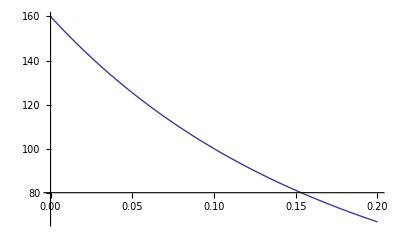

```mathematica
Plot[pv[{10,10,10,10,10,110},{1,2,3,4,5,6},r],{r,0.0,0.20}]
```

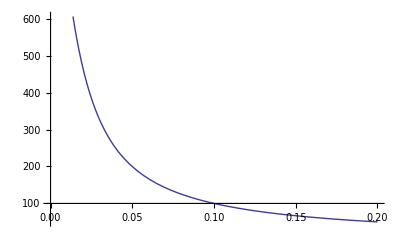

```mathematica
Plot[pv[Append[Table[10,{119}],110],Range[1,120],r],{r,0.0,0.20}]
```

ChapterLabel.Heading1  Constructing and Manipulating 
Yield Curves

Problem

You want to build a yield curve from underlying spot rates and then model changes in the curve so you can model the return of a portfolio of rate-sensitive securities.

Solution

If you are only interested in changes in the yield curve at a particular maturity, you can use published yields for various maturities and use interpolation. For example, here is some interest rate data taken from Bloomberg in late June 2009. The pairs are {days, rate}.

```mathematica
rates={{7,0.01},{14,0.04},{30,0.05},{60,0.17},{180,0.29},{360,0.4},{730,1.11},{1095,1.63},{1825,2.56},{2555,3.20},{3650,3.54},{5475,4.12},{7300,4.49},{10950,4.86}};
```

```mathematica
iRates =Interpolation[rates,Method->"Spline"];
```

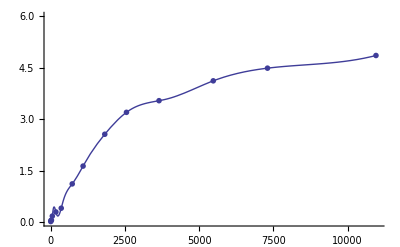

```mathematica
Show[ListPlot[rates,PlotStyle->{PointSize[0.01]},PlotRange->{{0,11000},{0,6}}],
Plot[iRates[t],{t,7,11000}]
]
```

Interpolation is all well and good, but if you want to understand the dynamics of the curve, you need a model. The Nelson-Siegel function is a popular parametric model of the yield curve.

```mathematica
nsYieldCurve[m_, β0_, β1_,β2_,τ_] := 
β0 + (β1(1-Exp[-m/τ]))/(m/τ)+ 
β2((1-Exp[-m/τ])/(m/τ) - Exp[-m/τ])
```

```mathematica
fit =FindFit[ rates, nsYieldCurve[m,b0,b1,b2,t],{b0,b1,b2,t},m,Method->NMinimize]
```

{b0→5.28846,b1→-5.26294,b2→-3.75868,t→651.468}

Here I use the fitted curve to initialize a Manipulate. You can then play with the parameters to get a feel for their effect.

```mathematica
Manipulate[Show[ListPlot[rates,PlotStyle->{PointSize[0.01]},PlotRange->{{0,11000},{0,6}}],Plot[nsYieldCurve[m,beta0,beta1,beta2,tau],{m,1,11000},PlotRange->{{0,11000},{0,6}}]],
{{beta0,b0},3,6,0.1},
{{beta1,b1},2,-6,0.1},
{{beta2,b2},-5,-1,0.1},
{{tau,t},100,1000,10},SaveDefinitions->True] /. fit
```

Discussion

An extension of the Nelson-Siegel model is the Svensson model, which addresses problems with convexity, inaccuracies introduced for large changes in yield due to the nonlinear relationship between prices and yields. The capital gain induced by a decline in the yield is larger than the capital loss induced by an equal-sized increase in the yield.

Given the Svensson model for the forward curve, you can use Mathematica’s symbolic integration capabilities to find the zero coupon (or spot) model.

```mathematica
Clear[svForwardCurve,svSpotCurve];
svForwardCurve[m_, β0_, β1_,β2_,β3_,τ1_,τ2_]:=β0+β1 Exp[-m/τ1] +β2(m/τ1)Exp[-m/τ1] + β3(m/τ2)Exp[-m/τ2]
```

```mathematica
svSpotCurve[m_, β0_, β1_, β2_, β3_, τ1_, τ2_] = 
  FullSimplify[(1/m)* Integrate[svForwardCurve[m, β0, β1, β2, β3, τ1, τ2], {m, 0, m}]]
```

(m β0+β1 (τ1-ⅇ^(-m/τ1) τ1)+β2 (τ1-ⅇ^(-m/τ1) (m+τ1))+β3 (τ2-ⅇ^(-m/τ2) (m+τ2)))/m

The solution demonstrates a so-called parametric method (i.e., a method based on parameters that have real-world meaning). There are also nonparametric methods that are in use where curves are fit using polynomials and tension splines. See the
following references.

See Also

This recipe is based on Parsimonious Modeling of Yield Curves by Charles R. Nelson and Andrew F. Siegel (Journal of Business, Vol. 60, No. 4 [Oct. 1987]: 473–489), which can be found online at http://bit.ly/1mQ3mq.

A library of Mathematica code for working with the term structure of interest rates can be found on Mark Fisher’s website at http://bit.ly/3hW4KC, with documentation at http://bit.ly/1ormSc.

A more thorough investigation of yield curve models can be found in this notebook at the Wolfram Library Archives, http://bit.ly/17OU4U, which was developed by Jan Hurt of the Charles University of Prague.

ChapterLabel.Heading1  Black-Scholes for European Option Pricing

Problem

You want to price European puts and calls using the Black-Scholes formula.

Solution

We give the solution to the Black-Scholes formula here without derivation. There are many excellent resources listed in the “See Also” section on page 572 for readers interested in the theory underlying this solution. The helper functions d1 and d2 have become fairly standard within the literature, so I use them here despite my personal aversion to short, cryptic names. The expression involving the d1 term in the pricing functions is related to the value of acquiring the stock; the expression involving the d2 term relates to the value of exercising the option on expiration.

```mathematica
Clear[d1, d2, priceEuroCall, priceEuroPut]
```

These helper functions are used by both priceEuroCall and priceEuroPut.

```mathematica
d1[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real] :=
(Log[price/strike]+(rate+volatility^2./2.)*maturityT)/(volatility*Sqrt[maturityT]);
d2[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real] :=
d1[price,strike,volatility,maturityT,rate]-volatility*Sqrt[maturityT];
cumNormDist[x_?NumberQ]:= CDF[NormalDistribution[],x];
```

Given the price of a stock, the strike price of the option, the volatility, time to option maturity in fractions of a year, and the risk-free interest rate, compute the value of a call or put option.

```mathematica
priceEuroCall[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real]:=price*cumNormDist[d1[price,strike,volatility,maturityT,rate]]-strike*Exp[-rate*maturityT]*cumNormDist[d2[price,strike,volatility,maturityT,rate]]
```

The fact that a put can be priced in terms of a call is called put-call parity.

```mathematica
priceEuroPut[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real]:=priceEuroCall[price,strike,volatility,maturityT,rate]+strike*Exp[-rate*maturityT]-price
```

Here we compute the value of a call option with strike $60 and 1/2 year to maturity, with the underlying stock trading at $70, with a volatility of 0.29, and a risk-free rate of 4%. The volatility is usually measured as the standard deviation of the stock price.

```mathematica
priceEuroCall[70.,60.,0.29,0.5,0.04]
```

12.6323

Here we show the opposing relationship between a call and a put with equal
attributes by plotting their values against the price of the underlying stock. A call
increases in value with the stock price, whereas a put decreases in value.

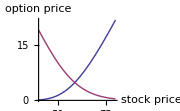

```mathematica
Plot[{priceEuroCall[s,60.,0.29,0.5,0.04],priceEuroPut[s,60.,0.29,0.5,0.04]},{s,40,80},PlotRange->All,AxesLabel->{"stock price","option price"},PlotRange->{{0,15},{2,15}},ImageSize->Small]
```

Discussion

Although the ability to price an option is vital to successful trading, it is equally vital to measure the sensitivity of an option (or any other derivative security) to changes in the economic environment. These measures are based on mathematical derivatives of the pricing function. These measures are collectively known as the Greeks because each is associated with a Greek letter.

```mathematica
Clear[deltaEuroCall,deltaEuroPut,gammaEuroCall,gammaEuroPut,thetaEuroCall,thetaEuroPut,rhoEuroCall,rhoEuroPut,vegaEuroCall,vegaEuroPut]
```

Delta is a measure of the sensitivity of an option to changes in the stock price. It is computed as the first derivative of the pricing function with respect to the underlying stock price.

```mathematica
deltaEuroCall[price_Real,strike_,volatility_Real,maturityT_Real,rate_Real] := 
Module[{s},D[priceEuroCall[s,strike,volatility,maturityT,rate],s] /. s:>price]
deltaEuroPut[price_Real,strike_,volatility_Real,maturityT_Real,rate_Real] := 
D[priceEuroPut[s,strike,volatility,maturityT,rate],s] /. s:>price
```

Gamma is a measure of the sensitivity of the delta to changes in the stock price. It is computed as the second derivative of the pricing function with respect to the underlying stock price.

```mathematica
gammaEuroCall[price_Real,strike_,volatility_,maturityT_,rate_] := 
Module[{s},D[priceEuroCall[s,strike,volatility,maturityT,rate],{s,2}] /. s:>price]
gammaEuroPut[price_Real,strike_,volatility_,maturityT_,rate_] :=
 Module[{s},D[priceEuroPut[s,strike,volatility,maturityT,rate],{s,2}] /. s:>price]
```

Theta is a measure of the sensitivity of the option price to time. It is computed as the first derivative of the pricing function with respect to the time to expiration (maturity).

```mathematica
thetaEuroCall[price_Real,strike_,volatility_Real,maturityT_Real,rate_Real] := 
Module[{t},-D[priceEuroCall[price,strike,volatility,t,rate],t] /. t:>maturityT]
thetaEuroPut[price_Real,strike_,volatility_Real,maturityT_Real,rate_Real] := 
Module[{t},-D[priceEuroPut[price,strike,volatility,t,rate],t] /. t:>maturityT]
```

Rho is a measure of the sensitivity of the option price to changes in the risk-free rate.  It is computed as the first derivative of the pricing function with respect to the interest rate.

```mathematica
rhoEuroCall[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real] := 
Module[{r},D[priceEuroCall[price,strike,volatility,maturityT,r],r] /. r:>rate]
rhoEuroPut[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real] := 
Module[{r},D[priceEuroPut[price,strike,volatility,maturityT,r],r] /. r:>rate]
```

Vega (also known as kappa) is a measure of the sensitivity of the option price to changes in the volatility.  It is computed as the first derivative of the pricing function with respect to the volatility.

```mathematica
vegaEuroCall[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real] := 
Module[{v},D[priceEuroCall[price,strike,v,maturityT,rate],v] /. v:>volatility]
vegaEuroPut[price_Real,strike_Real,volatility_Real,maturityT_Real,rate_Real] := 
Module[{v},D[priceEuroPut[price,strike,v,maturityT,rate],v] /. v:>volatility]
```

Here we compute delta of a call with strike $60 with 6 months left to maturity when the stock is trading at $40. This shows that the option will change value by roughly 3.7 cents for a dollar move. We can confirm this using the pricing function.

```mathematica
deltaEuroCall[40.00,60.,0.29,0.5,0.04]
```

0.0377654

This is in basic agreement with the difference between the value of the option at a stock price of $40.50 and $39.50 (we choose a dollar spread that places the delta stock price at the center).

```mathematica
priceEuroCall[40.50,60.,0.29,0.5,0.04] - priceEuroCall[39.50,60.,0.29,0.5,0.04]
```

0.0378454

You can get an intuitive feel for the behavior of options by creating a 3D plot of each Greek with respect to stock price and time.

Note how delta increases sharply as the stock price approaches the strike and how this sensitivity is stronger near expiration (t = 0).

```mathematica
Plot3D[deltaEuroCall[s,60.,0.29,t1,0.04],{s,40.,80.},{t1,0.001,1},ImageSize->Small]
```

-Graphics3D-

The sensitivity of the delta to shrinking time to maturity and strike price is reinforced by the plot of the gamma, which is the second derivative of the price, or the first derivative of the delta.

```mathematica
Plot3D[gammaEuroCall[s1,60.,0.29,t1,0.04],{s1,40.,80.},{t1,0.001,1.},ImageSize->Small]
```

-Graphics3D-

The plot of theta shows that the value of an option will decay more rapidly with adverse moves of the underlying stock when there is a short time to expiration compared to when there are longer times.

```mathematica
Plot3D[thetaEuroCall[s1,60,0.29,t1,0.04],{s1,40,80},{t1,0.001,1.},ImageSize->Small]
```

-Graphics3D-

```mathematica
Plot3D[rhoEuroCall[s1,60.,0.29,t1,0.04],{s1,40,80},{t1,0.001,1},ImageSize->Small]
```

-Graphics3D-

Note how sensitivity to volatility increases near the strike price and with increasing time. This follows from the fact that high volatility has more impact over longer time periods and for options that are in the money (because of the larger delta and gamma of in-the-money options).

```mathematica
Plot3D[vegaEuroCall[s1,60,0.29,t1,0.04],{s1,20,100},{t1,0.01,0.5},ImageSize->Small]
```

-Graphics3D-

The interactive capabilities of Mathematica 6 provide an excellent platform for getting the feel of the behavior of the Greeks. However, for sake of responsiveness, it is a good idea to evaluate the derivative outside the Manipulate. You can use With to evaluate the derivative before the call to Manipulate and FullSimplify to make sure it is in simplest form.

```mathematica
manipulateDeltaEuroCall[] :=Block[{k, v, t1, r},With[{deltaCall= FullSimplify[D[priceEuroCall[s, k, v, t1, r], s]]},Manipulate[Plot3D[Evaluate[deltaCall],{s,40.,80.},{t1,0.001,1.},PerformanceGoal->"Speed"],{{k,60.,"Strike"},10.,100.},{{r,0.04,"Rate"},0.01,0.12},{{v,0.29,"Volatility"},0.01,0.40},ContinuousAction->False,AppearanceElements->All]]]
```

```mathematica
manipulateDeltaEuroCall[]
```

See Also

Modeling Financial Derivatives with Mathematica (Cambridge University Press) by William Shaw is an excellent resource for the quant interested in modeling vanilla and more exotic flavors (such as Asian options) in Mathematica. It concentrates on analytical solutions rather than solutions based on numerical methods.

Black-Scholes and Beyond: Option Pricing Models by Neil A. Chris (McGraw-Hill) covers the basics of modern option pricing. Wikipedia also provides basic information on the Black-Scholes model: http://bit.ly/c8IrYX.

ChapterLabel.Heading1  Computing the Implied Volatility 
of Financial Derivatives

Problem

You want to compute the volatility of an option that is implied by its current market price.

Solution

Use FindRoot to solve for the volatility.

```mathematica
impliedVolEuroCall[price_,strike_,maturityT_,rate_,optionsPrice_]:=
volatility /. FindRoot[priceEuroCall[price,strike,volatility,maturityT,rate] == optionsPrice,{volatility,0.2}]
```

```mathematica
impliedVolEuroPut[price_,strike_,maturityT_,rate_,optionsPrice_]:=
volatility /. FindRoot[priceEuroPut[price,strike,volatility,maturityT,rate] == optionsPrice,{volatility,0.2}]
```

```mathematica
impliedVolEuroCall[58.00,60.,0.5,0.04,3.8]
```

0.254867

Discussion

Implied volatility is the volatility that is implied by the market price of the option given the pricing model. The idea is that the market will find the fair price for the option, and from that, you can back out the volatility of the underlying security that the market is pricing in. This is in contrast to historical volatility, which is a direct measure of the movement of the underlying’s price over recent history.

In the solution, FindRoot searches for a numerical root of the pricing function that will yield the observed price, given the other option parameters.

ChapterLabel.Heading1  Speeding Up NDSolve When Solving 
Black-Scholes and Other PDEs

Problem

You  want to compute numerical solutions to partial differential equations (PDEs), such as the Black-Scholes PDE. NDSolve can sometimes take too much time or lose accuracy near critical values. You would like to speed up NDSolve without loss of accuracy where it matters.

```mathematica
-D[u[x,t], t]==1/2 σ^2 x^2 D[u[x,t], x,x]+r x D[u[x,t], x]-r u[x,t];
```

Solution

This recipe was motivated by work done by Andreas Lauschke and used with permission. Refer to the “See Also” section on page 578 for more information.

To illustrate the problem, I use the PDE for a European put on a dividend-paying
security. For the interest and dividend, I use fixed rate plus time-varying rate that is strictly increasing. For volatility, I use a volatility smile, which reflects the observation that volatility is higher for in- and out-of-the-money options and lower for
at-the-money options. In the PDE, x represents the price of the underlying and t is time.

```mathematica
Clear[iRate,dividend,sigma,makePutEuropean];
iRate[t_]:= 0.035+t 0.01/3
dividend[t_] :=  0.01+t 0.01/3;
sigma[price_,strike_,time_] := 1./10000 (price-strike)^2+0.25
Options[makePutEuropean] = {Method->Automatic};
makePutEuropean[strike_,lower_,upper_,timeToExp_,opts:OptionsPattern[]]:=
Module[{},
NDSolve[{D[u[x,t],t]+1/2 D[u[x,t],x,x] x^2 sigma[x,strike,t]^2+
(iRate[t]-dividend[t]) x D[u[x,t],x]- iRate[t] u[x,t]== 0,
u[x,timeToExp]==Max[0,strike-x],
u[lower,t]==strike,
u[upper,t]==0},u,{x,lower,upper},{t,0,timeToExp},opts]]
```

You can adjust different aspects of this model to suit your needs. The main point here is to consider the performance of NDSolve using different options.

```mathematica
Off[NDSolve::"mxsst"]
{timePut1,put1}= makePutEuropean[50,0, 250, 1] //Timing
```

{3.01551,{{u→InterpolatingFunction[{{0.,250.},{0.,1.}},<>]}}}

It took just over eight seconds to solve this PDE numerically. However, you can do better using an adaptive grid method where you instruct NDSolve to sample more points around the strike price while being looser away from the strike. Here I define a function for the adaptive grid but defer explanation until the discussion.

```mathematica
Clear[makeAdaptiveGrid,makePutEuropeanAdaptive]
makeAdaptiveGrid[strike_,size_:200,deg_:1] := Module[{a = 2deg+1,incr= 2 strike/size}, Table[((x-strike)^a/strike^(a-1))+strike,{x,0,strike*2,incr}]]
```

```mathematica
makePutEuropeanAdaptive[strike_,lower_,upper_,timeToExp_]:=
Module[{},
NDSolve[{D[u[x,t],t]+1/2 D[u[x,t],x,x] x^2 sigma[x,strike,t]^2+
(iRate[t]-dividend[t]) x D[u[x,t],x]== iRate[t] u[x,t],
u[x,timeToExp]==Max[0,strike-x],
u[lower,t]==strike,
u[upper,t]==0},u,{x,lower,upper},{t,0,timeToExp},Method:> {"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","Coordinates"->N@Union[makeAdaptiveGrid[strike],Range[2 strike,5 strike,2]]}}]]
```

```mathematica
Off[NDSolve::"eerri",NDSolve::"eerr"]
{timePut2,put2}= makePutEuropeanAdaptive[50,0, 250, 1] //Timing
```

{0.129383,{{u→InterpolatingFunction[{{0.,250.},{0.,1.}},<>]}}}

You can see the speedup is quite substantial.

```mathematica
timePut1/timePut2
```

23.3068

Discussion

You can see that the result of pricing the option appears the same for both versions.

```mathematica
GraphicsColumn[{Plot3D[Evaluate[u[x,1-t]/.First@put1],{x,40,60},{t,0,1},PlotRange->All,ImageSize->{300,300},AxesLabel->{"Underlying Price","Time to\nExpiration","Option\nPrice"}],Plot3D[Evaluate[u[x,1-t]/.First@put2],{x,40,60},{t,0,1},PlotRange->All,ImageSize->{300,300},AxesLabel->{"Underlying Price","Time to\nExpiration","Option\nPrice"}]},Spacings->0]
```

-Graphics-

And, indeed, you can see that the max difference in both approaches is negligible.

```mathematica
Max@Flatten@Abs[Table[(u[x,t]/.First@put1),{x,40,60},{t,0,1,0.01}] -Table[(u[x,t]/.First@put2),{x,40,60},{t,0,1,0.01}]]
```

0.0000251351

A few words about the function makeAdaptiveGrid are in order. The motivation for this function can be seen considering the plot of  x^3.

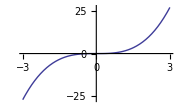

```mathematica
Plot[x^3,{x,-3,3},ImageSize->Small]
```

The slope about the origin is small compared to the slope at the extremes. This is perfect for our application because it means that simply shifting the origin to the strike will give a function that generates a dense grid around the strike and a looser one at the wings of the option (away from the strike). The two optional parameters of makeAdaptiveGrid control the number of grid points (size) generated and the
extent of the density around the slope (deg).

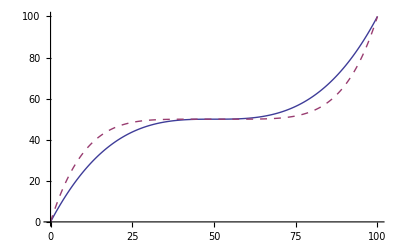

```mathematica
Needs["PlotLegends`"]
With[{strike=50},
ListLinePlot[{makeAdaptiveGrid[strike,200,1],makeAdaptiveGrid[strike,200,2]},DataRange->{0,2strike},PlotStyle->{Thin,Dashed},PlotLegend->{"deg = 1","deg = 2"},LegendPosition->{-0.75,0.25},LegendSize->0.5]]
```

In the NDSolve options, I use MethodOfLines, which is a very efficient way to numerically solve a PDE provided it is an initial value problem. In particular, the solution uses the suboption "SpatialDiscretization", which itself allows the coordinates to be passed in. Here the expression N@Union[makeAdaptiveGrid[strike], Range[2 strike, 5 strike, 2]] simply tacks on some coarsely spaced points far from the strike so we can ensure the solution is valid for a reasonably liberal range of prices on the high end. Refer to the references in the following “See Also” section for more details about MethodOfLines, which is quite feature rich and worth learning if you plan to use NDSolve.

See Also

This recipe was motivated by the notebook penalty.nb developed by Andreas Lauschke. The original notebook is available in the downloads section of this book’s website: http://bit.ly/xIgx7. Also see Lauschke’s site at http://bit.ly/1Zhdfv for useful Mathematica and web Mathematica samples, products, and services.

NDSolve was introduced in Recipe 13.9.

The MethodOfLines can be found in tutorial/NDSolvePDE in the Mathematica documentation.

ChapterLabel.Heading1  Developing an Explicit Finite Difference Method for the Black-Scholes Formula

Problem

You want to use the finite difference method (FDM) to compute solutions to the Black-Scholes formula in an efficient manner.

Solution

This solution was developed by Thomas Weber and rearranged to conform to the format of this book. Refer to the “See Also” section on page 582 for references to the original notebook.

In this solution we will price a European call option with the following attributes:

```mathematica
strike = 100.; (*strike price at maturity of the option*)
sigma = 0.2;    (*volatility of the prices of the underlying*) 
tau = 1.0;        (*time to maturity of the option*) 
rate   = 0.05 ; (*riskless interest rate*)
```

The presented calculation scheme is a version of the explicit finite difference method (FDM). While applying this calculation scheme, the new values for the derivative V_(j,i-1) are stepwise calculated from V_(j+1,i), V_(j,i), and V_(j-1,i). The concepts are elaborated in the “Discussion” section on page 580.

In this solution, the number of grid points for the discrete prices of the stock n can freely be chosen within a specific range. Increasing the number of time steps improves the accuracy but also increases the overall calculation time. For a first demonstration, the number of discrete stock prices is set to 20.

```mathematica
n = 20;
```

The grid points for the stock price should be placed in a range not too tight around the current stock price. In this example, the range is chosen from zero up to twice the strike price. From the chosen region results the step size ΔS for the discretization of the stock prices range. One way to generate the list of grid points is to use NestList. #+ΔS& within NestList is a generic function defined for local use.

On the list of discrete stock prices, the exercise function of the option can be applied. The resulting list provides the starting or initial values for the numerical method.

```mathematica
δS = (2*strike)/n;
S = NestList[#1 + δS & , 0, n]; 
V = (Max[#1 - strike, 0] & ) /@ S;
```

The necessary number of time steps for the explicit FDM to converge depends on the step size for the discretization of the stock price, the volatility, and the strike price. The number of time steps can be calculated as follows (for more information, see the Wilmott reference in the “See Also” section on page 582):

```mathematica
nt = Floor[τ/(δS/(2*X*σ))^2] + 1;
```

Then the size of the time steps are

```mathematica
δt = τ/nt;
```

In pricingFunc, two terms Γ and Δ (see the “Discussion” section on page 580) are the speed-critical computations since they are inside the Do loop. The Mathematica function ListConvolve is used because it is a very fast way to compute finite differences. After the Do loop is finished, V contains a list of option values. Each option value corresponds to a discrete stock price on the grid. Interpolation on these numbers produces an interpolating function for the option price given current price of the
underlying S_0.

```mathematica
pricingFunc[X_, r_, t_, σ_, n_] := 
Module[{Δ, Γ, s, v, V, S, δS}, δS = (2*X)/n; 
S = NestList[#1 + δS & , 0, n];
V = (Max[#1 - X, 0] & ) /@ S; 
Do[Δ = ListConvolve[{1, 0, -1}, V]/(2*δS);
Γ = ListConvolve[{1, -2, 1}, V]/δS^2; 
      s = Take[S, {2, -2}]; 
v = Take[V, {2, -2}]; 
V = Join[{0}, v + δt*((1/2)*σ^2*s^2*Γ + r*s*Δ - r*v), 
        {Last[S] - X/E^(r*i*δt)}], {i, nt}
]; 
Interpolation[Transpose[{S, V}]]]
```

```mathematica
pf =pricingFunc[V,S,X,r,δS,δt,σ,nt];
S0 = 100.;   (*price of the stock at valuation time*)
pf[S0]
```

pricingFunc[{0,0,0,0,0,0,0,0,0,0,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.},{0,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.},X,r,10.,τ/(1+Floor[0.04 X^2 σ^2 τ]),σ,1+Floor[0.04 X^2 σ^2 τ]][100.]

Discussion

The PDE from the Black-Scholes formula for a derivative V on the security S is given as:

```mathematica
Clear[S, δS, t, δt, σ, r, V];
pde = -D[V[S, t], t] == 
(1/2)*σ^2*S^2*D[V[S, t], S, S] + r*S*D[V[S, t], S] - r*V[S, t];
```

Numerical approximation for the partial derivative follows, for example from the Taylor series. The partial derivatives in the equation are replaced through the appropriate Taylor series.

```mathematica
rls = {D[V[S, t], t] -> (V[S, t - δt] - V[S, t])/δt, 
D[V[S, t], S] -> (V[S + δS, t] - V[S - δS, t])/(2*δS),
D[V[S, t], S, S] -> (V[S + δS, t] - 2*V[S, t] + V[S - δS, t])/δS^2};
 prox = pde /. rls
```

-(-V[S,t]+V[S,t-δt])/δt==-r V[S,t]+(r S (-V[S-δS,t]+V[S+δS,t]))/(2 δS)+(S^2 σ^2 (-2 V[S,t]+V[S-δS,t]+V[S+δS,t]))/(2 δS^2)

In the next step, the notation is changed to make it more consistent with a grid scheme.

```mathematica
prox = prox /.{V[S,t] -> Subscript[V, j,i],V[S,t-δt] -> Subscript[V, j,i-1],V[S+δS,t] -> Subscript[V, j+1,i],V[S-δS,t] -> Subscript[V, j-1,i]}
```

-(V_(j,-1+i)-V_(j,i))/δt==-r V_(j,i)+(r S (-V_(-1+j,i)+V_(1+j,i)))/(2 δS)+(S^2 σ^2 (V_(-1+j,i)-2 V_(j,i)+V_(1+j,i)))/(2 δS^2)

To better illustrate the structure of the equation, more notational adjustments are made. The new structure will later help to simplify the calculations.

```mathematica
prox = prox /.  {(Subscript[V, j+1,i]-2 Subscript[V, j,i]+Subscript[V, j-1,i])/δS^2-> Subscript[Γ, i,j],(Subscript[V, j+1,i]-Subscript[V, j-1,i])/(2δS)-> Subscript[Δ, i,j]}
```

-(V_(j,-1+i)-V_(j,i))/δt==-r V_(j,i)+1/2 S^2 σ^2 Γ_(i,j)+r S Δ_(i,j)

Solving the last expression for V_(j,i) and simplifying leads to

```mathematica
diff = Solve[prox,Subscript[V, j,i-1]] // Simplify // First;
diff // TraditionalForm
```

{V_(j,i-1)→(r δt+1) V_(j,i)-1/2 S δt (2 r Δ_(i,j)+S σ^2 Γ_(i,j))}

The presented calculation scheme is a version of the explicit FDM. While applying this calculation scheme, the new values for the derivative V_(j,i-1) are stepwise calculated from V_(j+1,i), V_(j,i), and V_(j-1,i). Figure 14-1 illustrates this approach.

Explicit FDM

An efficient Mathematica function for the calculation of the differences needed in Δ and Γ is available through ListConvolve. To demonstrate this, ListConvolve is
applied to a list of symbols.

```mathematica
Clear[V,δS];
v= Table[Subscript[V, j],{j,6}]
```

{V_1,V_2,V_3,V_4,V_5,V_6}

ListConvolve used for Δ results in the following expression.

```mathematica
Δ = ListConvolve[{1, 0, -1}, v]/(2 δS) // TraditionalForm
```

{(V_3-V_1)/(2 δS),(V_4-V_2)/(2 δS),(V_5-V_3)/(2 δS),(V_6-V_4)/(2 δS)}

The first list in ListConvolve, the kernel {1,0,1}, is applied piecewise to the second list, multiplies the elements of the second list, and adds them up according to the values given in the kernel. This operation runs internally in Mathematica and is much faster than any loop written in Mathematica code.

The approach used for Δ can also be applied for the calculation of Γ. ListConvolve can replace loops that are common to the explicit approximation of PDEs.

```mathematica
Γ = ListConvolve[{1, -2, 1}, v] / (δS ^ 2) // TraditionalForm
```

{(V_1-2 V_2+V_3)/δS^2,(V_2-2 V_3+V_4)/δS^2,(V_3-2 V_4+V_5)/δS^2,(V_4-2 V_5+V_6)/δS^2}

See Also

Derivatives: The Theory and Practice of Financial Engineering (Wiley) by P. Wilmott contains the technical background underlying this recipe.

This recipes was derived from work done by Thomas Weber of Weber & Partner. The original notebook and other interesting financial applications in Mathematica can be found at http://bit.ly/bR0bF.

The method used in this recipe is based on the explicit FDM. There are also implicit methods. See Wikipedia for a general explanation of the difference and the trade-offs (http://bit.ly/tr3IN).

ChapterLabel.Heading1  Compiling an Implementation of Explicit Trinomial for Fast Pricing of American Options

Problem

You need a very fast pricer for American options. You want to make sure the implementation can be compiled for fastest possible execution without any calls to noncompiled code.

Solution

This solution was contributed by Andreas Lauschke. See Recipe 14.8 for more information.

Mathematica has a built-in compiler that creates optimized code for a Mathematica-specific virtual machine. Compile is discussed fully in Recipe 18.5. Here we simply show an application that creates a pricer for American options using trinomial scheme (see discussion).

```mathematica
americanPutCompiled=Compile[{kk,r,sigma,tt},
With[{a=5,nn=100,mm=20,tt0=sigma^2 tt/2,k=2 r/sigma^2},
Module[{alpha,h=2 a/nn,s=tt0/mm,x,ss,tmax,f,pp0,u,z},
alpha=s/h^2;
x=Range[-a,a,h];
ss=kk Exp@x;
tmax=MapThread[Max,{Table[0,{nn+1}],1-Exp@x}];
f=Exp[1/2 (k-1) x+1/4 (k+1)^2 (#-1) s] tmax&/@Range[mm+1];
pp0=Max[0,kk-#]&/@ss;
u=Exp[1/2 (k-1) x] pp0/kk;
Do[z=alpha (Take[u,{3,nn+1}]+Take[u,{1,nn-1}])-(2 alpha-1) Take[u,{2,nn}];
z=Append[Prepend[z,alpha u[[2]]-(2 alpha-1) u[[1]]+alpha/kk Exp[1/2 (k-1) a+1/4 (k+1)^2 (j-1) s]],0];
u=MapThread[Max,{z,f[[j]]}];,{j,mm}];
{ss,kk Exp[-1/4 (k+1)^2 tt0] Exp[-1/2 (k-1) x] u}]]];
```

You can see that 10 runs of the pricer over various strike prices execute in 32 milliseconds.

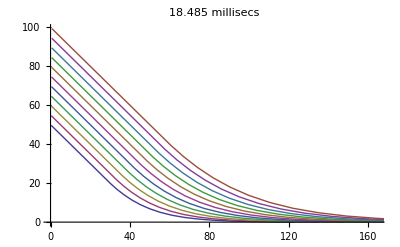

```mathematica
{time,pricing} =Timing[Table[Take[Transpose@americanPutCompiled[strike,0.05,0.4,1],60],{strike,50,100,5}]];
ListLinePlot[pricing,PlotLabel-> ToString[time*10^3] <> " millisecs"]
```

Discussion

The function americanPutCompiled returns a packed array of two lists: the first is a list of nodes in the spatial (stock price) direction, and the second is a list of American option prices at these nodes. The two lists can now be interpolated with Mathematica’s Interpolation function to obtain intermediate values.

The function americanPutCompiled is fully compiled, as can be seen by inspecting americanPutCompiled[[4]] and noting that all list elements are numeric.

```mathematica
DeleteCases[Flatten[americanPutCompiled[[4]]],_?NumericQ]
```

{}

The algorithm implements a method to price American options based on the linear complementarity formulation of the free boundary value problem. The numbers a, nn, T0, and mm (and, correspondingly, s and h) are parameters that define the grid to be used. a and nn determine the grid along the space (stock price) axis, and T0 and mm determine the grid along the time axis. For explicit methods, it is crucial to keep the spatial and temporal spacing in certain limits, otherwise local blow-up will occur. For a 100% explicit method, it is necessary that alpha=s/h^2<=1/2. That means that if the spatial step size h is reduced by a factor of 10, the time step size s has to be reduced by a factor of 100. This is not due to reasons of precision, but due to reasons of stability. If, for example, mm is lowered to 15, alpha is no longer <=1/2, and the instability becomes quite visible. For numbers like 5 or 10 for mm, the method wreaks

havoc. Traditional American option pricing methods use binomial trees and exhibit this problem with what is called oscillations. (All tree methods are necessarily 100% explicit.) It’s the same stability problem that is inherent to all explicit methods.

What makes this rectangular grid method so powerful is the fact that although it is faster than most tree-based implementations, it computes the option prices for the whole interval, not just for one particular price of the underlying, which is a limitation all tree-based methods possess.

See Also

Recipe 18.5 explains the mechanics of compiled functions and the performance implications of functions that don’t fully compile.

See Ansgar Jüngel, “Modellierung und Numerik von Finanzderivaten,” Vorlesungsmanuskript 2002, Johannes-Gutenberg Universität Mainz.

ChapterLabel.Heading1  Modeling the Value-at-Risk of a Portfolio Using Monte Carlo and Other Methods

Problem

You want to understand the worst expected loss of a portfolio of securities. This is referred to as Value-at-Risk or VaR. Specifically, you want to use Monte Carlo methods because these allow you to trade accuracy for speed by varying the number of samples.

Since the financial disaster that began in 2007, the notion of Value-at-Risk has become quite controversial. Some, like Nassim Taleb, have called it an intellectual fraud, while others have called it an invaluable tool, if used properly. I include this recipe as an illustration of the math behind one particular implementation of VaR and without judgment as to its effectiveness. Please refer to the link in the “See Also” section on page 587 for a thorough discussion of the efficacy of VaR in practice.

Solution

In its simplest form, VaR is a measure of the worst expected loss under normal market conditions over some time interval, usually days or weeks. The simplest (and highly artificial) illustration of VaR concerns a portfolio consisting of a single security. Let’s assume it is worth $10 million, the average return is 0.085, and the standard deviation is 0.26. The distribution of the portfolio’s value is

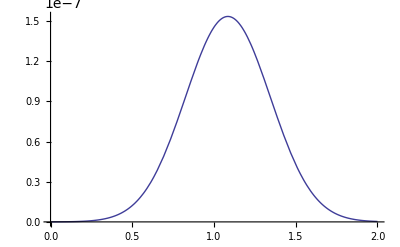

```mathematica
With[{portfolio=10^7,return = 0.085,stddev = 0.26},
Plot[PDF[NormalDistribution[portfolio * (1.0 + return), portfolio *stddev ],x],{x,0,2 portfolio}]]
```

From this we can compute the probability of a loss of 25% using the CDF.

```mathematica
With[{portfolio=10000000,return = 0.085,stddev = 0.26,loss = 0.25},CDF[NormalDistribution[portfolio * (1.0 + return), portfolio *stddev ], portfolio  (1-loss)]]
```

0.0987927

VaR is computed in terms of worst expected loss in dollars at a certain probability level, say 1%.

```mathematica
valueAtRisk[startingValue_,meanReturn_, var_, level_] := 
Module[{expected =startingValue* (1+ meanReturn)},
startingValue -  Quantile[NormalDistribution[expected,startingValue*var],level]]
```

```mathematica
With[{portfolio=10000000,meadReturn = 0.085,stddev = 0.26,loss = 0.25},
valueAtRisk[portfolio, meadReturn,stddev,0.01]]
```

5.1985×10^6

Thus the VaR at 1% is about 5.2 million.

Discussion

The solution merely shows the statistical ideas behind VaR. In real-life scenarios, portfolios are more complexly structured, and you need to measure and account for correlations in the movements of these assets’ values. The rest of this discussion deals with these issues.

The first issue to address is that prices don’t typically follow a NormalDistribution but rather a LogNormal one. Second, portfolio managers and traders are typically interested in VaR over much shorter time periods than one year. So a more useful function is

```mathematica
Clear[valueAtRisk]
valueAtRisk[startingValue_,mean_, var_, level_, days_,tradingDays_:365]:=
	Module[{T = days/tradingDays},
startingValue - Exp[Quantile[NormalDistribution[Log@startingValue+ (mean - var^2/2)*T,var*T],level]]
]
```

Here we compute the VaR assuming 250 trading days.

```mathematica
With[{portfolio=10000000,return = 0.085,stddev = 0.26,loss = 0.25,days=1},
valueAtRisk[portfolio, return, stddev,0.01,days,250]]
```

22121.5

See Also

An extensive discussion of VaR in light of the financial crisis of 2007–2009 (and counting) can be found in this excellent New York Times article by Joe Nocera:
http://bit.ly/2SgV68.

ChapterLabel.Heading1  Visualizing Trees for Interest-Rate 
Sensitive Instruments

Problem

You are using a tree-based approach to pricing (such as the Hull-White trees) and you want to visualize these trees using Mathematica’s graphics abilities. Such visualizations are often useful for pedagogical or diagnostic purposes.

Solution

In this recipe, I am only concerned with using Mathematica for visualizing Hull-White trees. See the “See Also” section on page 591 for the theory and Mathematica implementation of the same for pricing purposes.

The usual way to implement tree valuation methods is to state results in two or more new states, thereby modeling the diffusion of the stochastic process. The idea of Hull-White to model mean reverting processes is to add boundary conditions to this tree structure. The boundary conditions are valid for a given maximum state.

The graphical building blocks of the tree can then be defined as follows. The variable nmax is global. There are three primitive elements: a nonboundary element, an upper-boundary element, and a lower-boundary element. The function path returns a triple that defines the terminal points of the path.

```mathematica
path[j_] :=j+{1,0,-1}
path[j_ /; j ==nmax] :=j-{0,1,2}
path[j_ /; j ==-nmax] :=j+{0,1,2}
```

The function grpath then constructs the graphical representation in terms of Line elements emanating from a starting point.

```mathematica
grpath[pt:{i_,j_}] :=Line[{pt,{i+1,#}}]& /@ path[j]
```

Here then are the three primitive components used to build the tree.

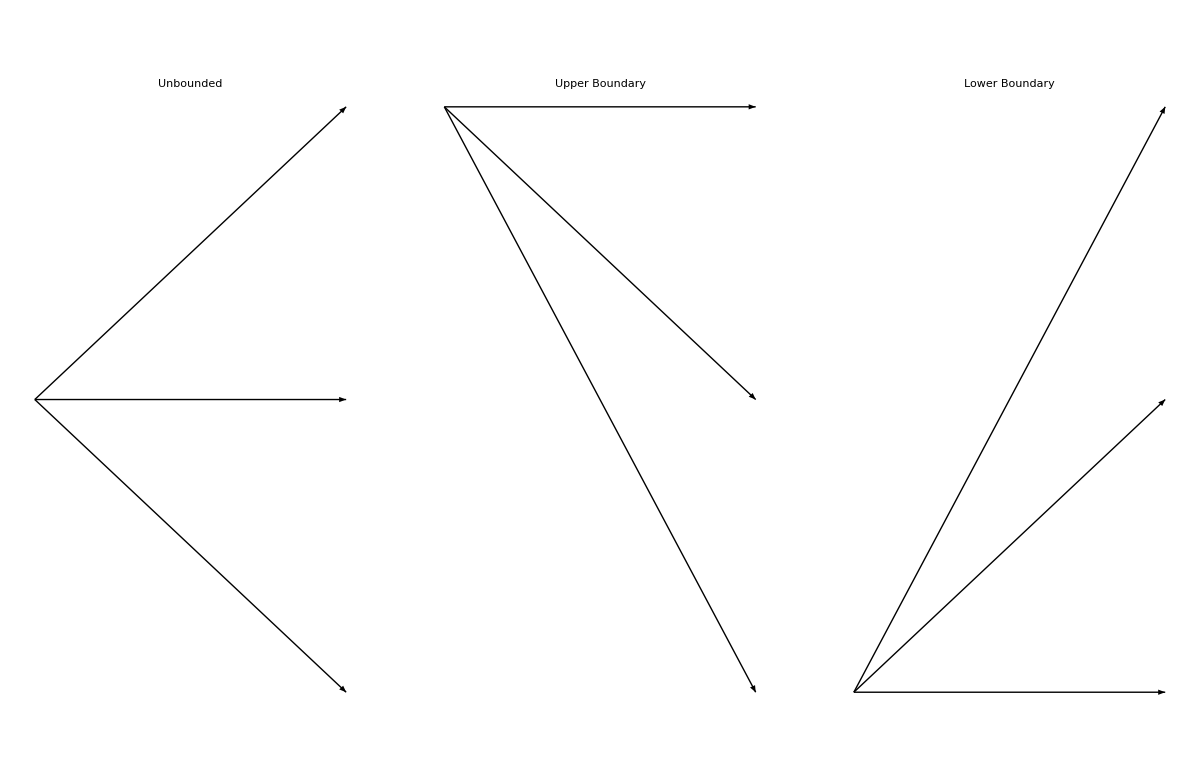

```mathematica
Block[{nmax=2},
GraphicsGrid[{{Graphics[grpath[{0,1}],PlotLabel->"Unbounded"],
Graphics[grpath[{0,nmax}],PlotLabel->"Upper Boundary"],
Graphics[grpath[{0,-nmax}],PlotLabel->"Lower Boundary"]}},
AspectRatio ->0.3]/.Line->Arrow]
```

Given these primitives, it’s a straightforward process to generate a tree with a particular boundary and depth.

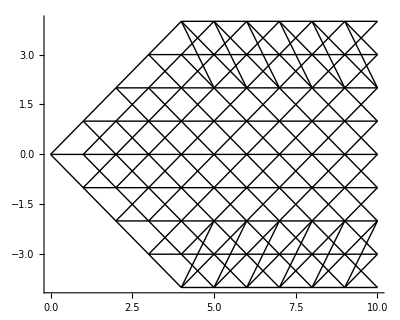

```mathematica
Block[{nmax=4,depth=10},
Module[{n},
n[m_]:=Min[nmax,m];
Graphics[Table[grpath[{m,j}],{m,0,depth-1},{j,-n[m],n[m]}],Axes->True]]]
```

Discussion

The solution is really just a skeleton to illustrate the general technique. For purposes of visualization, we need trees with labels that suggest the underlying semantics of Hull-White. A particularly nice way to proceed is to augment the tree with node
labels that are purely coordinates. This is just a matter of adding text elements to the solution version. The resulting gr becomes a template, and you can leverage Mathematica’s pattern-directed replacement to assign meaningful labels to the nodes.

```mathematica
gr = Block[{nmax=2,depth=3},
Module[{n },
n[m_]:=Min[nmax,m];
Flatten[Table[{If[m<depth,grpath[{m,j}],{}],
Text[{m,j},{m,j},Background->White]},{m,0,depth},{j,-n[m],n[m]}]]
]];
```

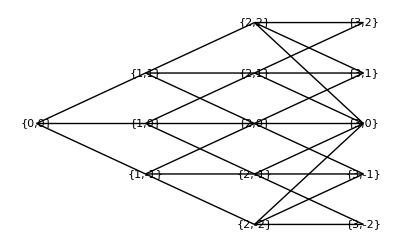

```mathematica
Graphics[gr,AspectRatio->1/GoldenRatio]
```

The process you want to visualize is a single-factor interest rate model described by the following formula:

```mathematica
dr = (θ(t) - a Subscript[r, t] )dt + σ dz.
```

Here r is the short-term rate, and a and σ are constants.

```mathematica
a = 0.1;
σ = 0.01; 
Δt = 1; 
Δr = σ*Sqrt[3*Δt];
```

Using the template gr, replace the nodes with the rate deltas using the node coordinates in the computation of the labels. Here you use depth Infinity with Replace so you need not worry about the actual depth of the graphics elements.

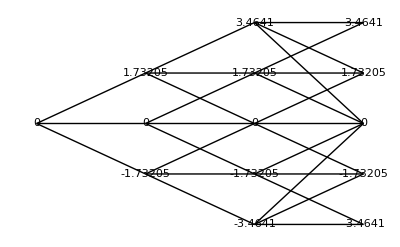

```mathematica
Graphics[Replace[gr,{{x_Integer,y_Integer}:>{x,y Δr},
Text[{m_,j_},y___]:>Text[j 100 ,y]},Infinity],
AspectRatio->1/GoldenRatio]
```

See Also

This recipe contains content originally developed by Thomas Weber of Weber & Partner (http://bit.ly/3Dz1wg) and is used with permission. A complete notebook showing both the theory and visualization is available at this cookbook’s website: http://bit.ly/xIgx7.